```mathematica
eq={u u + v v==1,F==u v};Solve[eq,{u,v}]
```

{{u→(-(√(1-√(1-4 F^2)))/(2 √2)-(√(1-4 F^2) √(1-√(1-4 F^2)))/(2 √2))/F,v→-(√(1-√(1-4 F^2)))/(√2)},{u→((√(1-√(1-4 F^2)))/(2 √2)+(√(1-4 F^2) √(1-√(1-4 F^2)))/(2 √2))/F,v→(√(1-√(1-4 F^2)))/(√2)},{u→(1/2 √(1/2+1/2 √(1-4 F^2))-1/2 √(1-4 F^2) √(1/2+1/2 √(1-4 F^2)))/F,v→√(1/2+1/2 √(1-4 F^2))},{u→(-1/2 √(1/2+1/2 √(1-4 F^2))+1/2 √(1-4 F^2) √(1/2+1/2 √(1-4 F^2)))/F,v→-√(1/2+1/2 √(1-4 F^2))}}

```mathematica
{u u,v v}/.%
```

{{((-(√(1-√(1-4 F^2)))/(2 √2)-(√(1-4 F^2) √(1-√(1-4 F^2)))/(2 √2))^2)/F^2,1/2 (1-√(1-4 F^2))},{(((√(1-√(1-4 F^2)))/(2 √2)+(√(1-4 F^2) √(1-√(1-4 F^2)))/(2 √2))^2)/F^2,1/2 (1-√(1-4 F^2))},{((1/2 √(1/2+1/2 √(1-4 F^2))-1/2 √(1-4 F^2) √(1/2+1/2 √(1-4 F^2)))^2)/F^2,1/2+1/2 √(1-4 F^2)},{((-1/2 √(1/2+1/2 √(1-4 F^2))+1/2 √(1-4 F^2) √(1/2+1/2 √(1-4 F^2)))^2)/F^2,1/2+1/2 √(1-4 F^2)}}

```mathematica
D[%,F]
```

{{1/F^2 2 (-F/(√2 √(1-√(1-4 F^2)))-F/(√2 √(1-4 F^2) √(1-√(1-4 F^2)))+(√2 F √(1-√(1-4 F^2)))/(√(1-4 F^2))) (-(√(1-√(1-4 F^2)))/(2 √2)-(√(1-4 F^2) √(1-√(1-4 F^2)))/(2 √2))-(2 (-(√(1-√(1-4 F^2)))/(2 √2)-(√(1-4 F^2) √(1-√(1-4 F^2)))/(2 √2))^2)/F^3,(2 F)/(√(1-4 F^2))},{1/F^2 2 (F/(√2 √(1-√(1-4 F^2)))+F/(√2 √(1-4 F^2) √(1-√(1-4 F^2)))-(√2 F √(1-√(1-4 F^2)))/(√(1-4 F^2))) ((√(1-√(1-4 F^2)))/(2 √2)+(√(1-4 F^2) √(1-√(1-4 F^2)))/(2 √2))-(2 ((√(1-√(1-4 F^2)))/(2 √2)+(√(1-4 F^2) √(1-√(1-4 F^2)))/(2 √2))^2)/F^3,(2 F)/(√(1-4 F^2))},{1/F^2 2 (F/(2 √(1/2+1/2 √(1-4 F^2)))-F/(2 √(1-4 F^2) √(1/2+1/2 √(1-4 F^2)))+(2 F √(1/2+1/2 √(1-4 F^2)))/(√(1-4 F^2))) (1/2 √(1/2+1/2 √(1-4 F^2))-1/2 √(1-4 F^2) √(1/2+1/2 √(1-4 F^2)))-(2 (1/2 √(1/2+1/2 √(1-4 F^2))-1/2 √(1-4 F^2) √(1/2+1/2 √(1-4 F^2)))^2)/F^3,-(2 F)/(√(1-4 F^2))},{1/F^2 2 (-F/(2 √(1/2+1/2 √(1-4 F^2)))+F/(2 √(1-4 F^2) √(1/2+1/2 √(1-4 F^2)))-(2 F √(1/2+1/2 √(1-4 F^2)))/(√(1-4 F^2))) (-1/2 √(1/2+1/2 √(1-4 F^2))+1/2 √(1-4 F^2) √(1/2+1/2 √(1-4 F^2)))-(2 (-1/2 √(1/2+1/2 √(1-4 F^2))+1/2 √(1-4 F^2) √(1/2+1/2 √(1-4 F^2)))^2)/F^3,-(2 F)/(√(1-4 F^2))}}

```mathematica
FullSimplify[%,F>0]
```

{{(√(1-√(1-4 F^2)))/(√(2-8 F^2)),-F/(√(1/2-2 F^2) √(1-√(1-4 F^2)))},{-(√(1-√(1-4 F^2)))/(√(2-8 F^2)),F/(√(1/2-2 F^2) √(1-√(1-4 F^2)))},{(√(1+√(1-4 F^2)))/(√(2-8 F^2)),-F/(√(1/2-2 F^2) √(1+√(1-4 F^2)))},{-(√(1+√(1-4 F^2)))/(√(2-8 F^2)),F/(√(1/2-2 F^2) √(1+√(1-4 F^2)))}}

```mathematica
FullSimplify[%,F<1/2]
```

{{(√(1-√(1-4 F^2)))/(√(2-8 F^2)),-F/(√(1/2-2 F^2) √(1-√(1-4 F^2)))},{-(√(1-√(1-4 F^2)))/(√(2-8 F^2)),F/(√(1/2-2 F^2) √(1-√(1-4 F^2)))},{(√(1+√(1-4 F^2)))/(√(2-8 F^2)),-F/(√(1/2-2 F^2) √(1+√(1-4 F^2)))},{-(√(1+√(1-4 F^2)))/(√(2-8 F^2)),F/(√(1/2-2 F^2) √(1+√(1-4 F^2)))}}

```mathematica
D[((1+2F)^(1/2)-(1-2F)^(1/2))^2/4,F]
```

1/2 (1/(√(1-2 F))+1/(√(1+2 F))) (-√(1-2 F)+√(1+2 F))

```mathematica
FullSimplify[%,F>0]
```

(2 F)/(√(1-4 F^2))

```mathematica
5!
```

120

```mathematica
F[M_,N_,L_]:=M!(N+M-L)!/((M-L)!(N+M)!)
```

```mathematica
P[NN_,L_]:=N[(NN!)/((NN-L)!(L!))];S[N_,M_,L_,A_]:=(P[N,A]*P[M,L-A])/P[M+N,L];
SS[N_,M_,L_,A_]:=S[N,M,L,A]/((N+M)^A)
```

```mathematica
N[S[30000,500000,1000,Range[0,209]]]
```

{4.67245×10^-26,2.80908×10^-24,8.43538×10^-23,1.68695×10^-21,2.52762×10^-20,3.02663×10^-19,3.017×10^-18,2.57508×10^-17,1.92116×10^-16,1.27271×10^-15,7.58026×10^-15,4.10009×10^-14,2.03076×10^-13,9.27488×10^-13,3.92932×10^-12,1.55206×10^-11,5.74135×10^-11,1.9968×10^-10,6.55201×10^-10,2.03458×10^-9,5.99574×10^-9,1.68098×10^-8,4.49386×10^-8,1.14792×10^-7,2.80713×10^-7,6.58301×10^-7,1.48283×10^-6,3.21298×10^-6,6.70606×10^-6,0.0000134997,0.0000262421,0.0000493137,0.0000896778,0.00015797,0.000269796,0.000447139,0.000719697,0.00112588,0.00171312,0.00253708,0.00365947,0.00514411,0.00705132,0.00943066,0.0123129,0.0157018,0.019567,0.023839,0.0284078,0.0331254,0.0378129,0.0422712,0.0462961,0.0496933,0.052295,0.0539733,0.0546509,0.0543068,0.0529764,0.050747,0.0477487,0.0441426,0.0401065,0.0358216,0.0314598,0.0271741,0.0230911,0.0193073,0.0158886,0.0128714,0.0102669,0.00806506,0.00624051,0.00475728,0.00357359,0.00264568,0.00193078,0.00138921,0.000985622,0.000689661,0.000476005,0.000324119,0.000217762,0.00014438,0.0000944801,0.0000610303,0.0000389208,0.000024508,0.0000152398,9.35945×10^-6,5.67778×10^-6,3.40263×10^-6,2.01471×10^-6,1.17875×10^-6,6.8154×10^-7,3.89467×10^-7,2.19992×10^-7,1.22843×10^-7,6.78171×10^-8,3.7019×10^-8,1.99824×10^-8,1.06672×10^-8,5.6322×10^-9,2.9415×10^-9,1.51972×10^-9,7.76792×10^-10,3.92851×10^-10,1.96595×10^-10,9.73586×10^-11,4.77169×10^-11,2.31474×10^-11,1.11147×10^-11,5.28317×10^-12,2.48615×10^-12,1.15832×10^-12,5.34357×10^-13,2.441×10^-13,1.10426×10^-13,4.94733×10^-14,2.19532×10^-14,9.64901×10^-15,4.20102×10^-15,1.81194×10^-15,7.74242×10^-16,3.2778×10^-16,1.37496×10^-16,5.71512×10^-17,2.35405×10^-17,9.60919×10^-18,3.88745×10^-18,1.55875×10^-18,6.19504×10^-19,2.44059×10^-19,9.53133×10^-20,3.69013×10^-20,1.4164×10^-20,5.39022×10^-21,2.03389×10^-21,7.60978×10^-22,2.82333×10^-22,1.03877×10^-22,3.79022×10^-23,1.37158×10^-23,4.92275×10^-24,1.75245×10^-24,6.1881×10^-25,2.1675×10^-25,7.53138×10^-26,2.59609×10^-26,8.87804×10^-27,3.0122×10^-27,1.014×10^-27,3.38687×10^-28,1.1225×10^-28,3.69159×10^-29,1.20477×10^-29,3.90185×10^-30,1.2541×10^-30,4.00044×10^-31,1.26652×10^-31,3.9798×10^-32,1.24129×10^-32,3.84293×10^-33,1.18099×10^-33,3.6028×10^-34,1.09109×10^-34,3.28033×10^-35,9.79114×10^-36,2.90148×10^-36,8.53671×10^-37,2.4938×10^-37,7.23349×10^-38,2.08335×10^-38,5.95826×10^-39,1.69213×10^-39,4.77219×10^-40,1.33655×10^-40,3.7175×10^-41,1.0269×10^-41,2.81725×10^-42,7.67647×10^-43,2.07753×10^-43,5.58462×10^-44,1.49113×10^-44,3.95477×10^-45,1.0419×10^-45,2.72675×10^-46,7.089×10^-47,1.83088×10^-47,4.69764×10^-48,1.19745×10^-48,3.03252×10^-49,7.63012×10^-50,1.90744×10^-50,4.73773×10^-51,1.16924×10^-51,2.86723×10^-52,6.98642×10^-53,1.69158×10^-53,4.06991×10^-54,9.7307×10^-55,2.31195×10^-55,5.45883×10^-56,1.2809×10^-56,2.98703×10^-57,6.92273×10^-58,1.59456×10^-58,3.65039×10^-59,8.3058×10^-60,1.87835×10^-60}

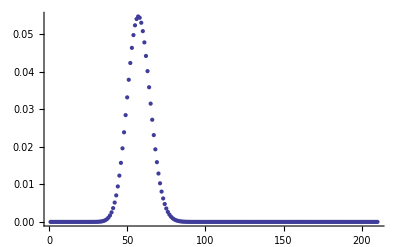

```mathematica
ListPlot[%]
```

```mathematica
P[5,4]
```

120

```mathematica
P[25,4]
```

303600